```mathematica
Import["E:\study\PROJECTS\MISC\Indoor-Mapping-Generator\floorplan_images"]
```

Import::nffil: File not found during Import.

$Failed

```mathematica
Import["E:\\study\\PROJECTS\\MISC\\Indoor-Mapping-Generator\\floorplan_images\\2d_floorplan.jpg"]
```

-Graphics-

```mathematica
EdgeDetect[-Graphics-]
```

-Graphics-

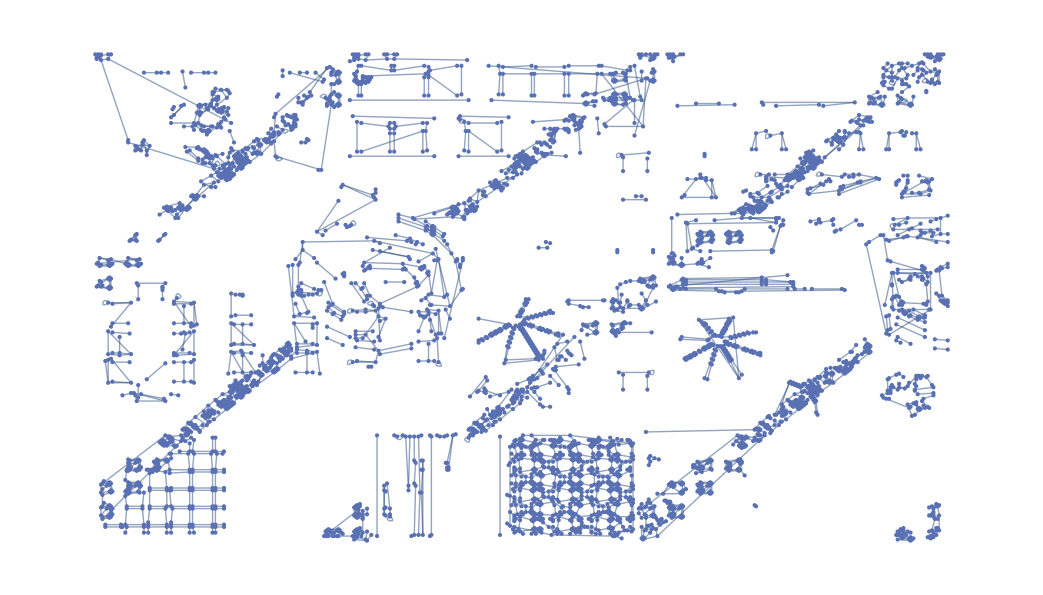

```mathematica
MorphologicalGraph[-Graphics-]
```

```mathematica
EdgeCount[%8]
```

5482

```mathematica
WeightedGraphQ[%8]
```

True

```mathematica
ConnectedGraphQ[%8]
```

```mathematica
False
```

False

```mathematica
EdgeCount[-Graphics-]
```

```mathematica
5482
```

5482

```mathematica
EdgeDetect[-Graphics-]
```

-Graphics-

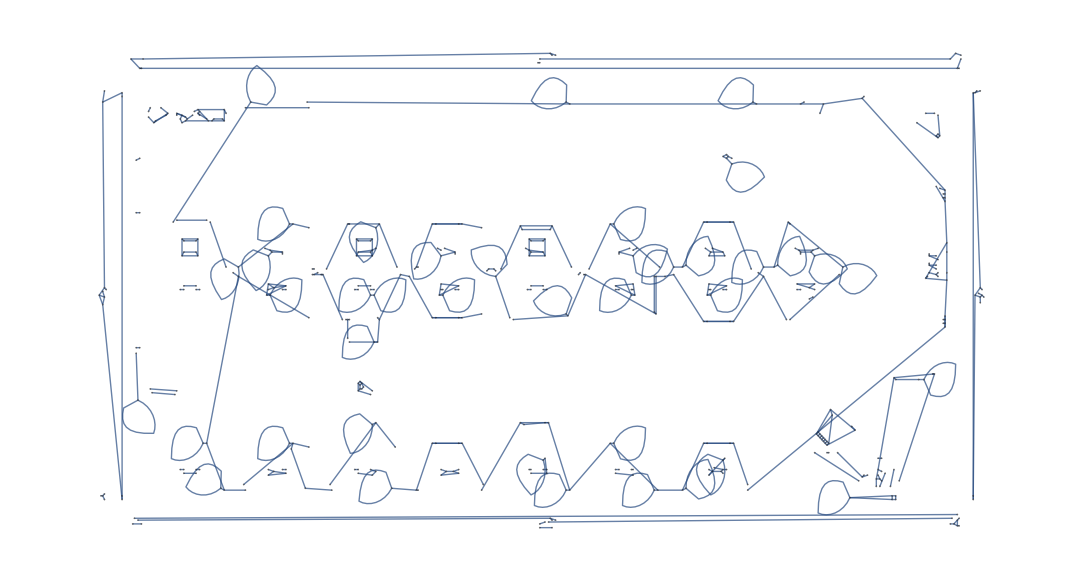

Set::write: Tag Inherited in Inherited[State] is Protected.

```mathematica
MorphologicalGraph[-Graphics-]
```

```mathematica
c=EdgeCount[-Graphics-]
```

528

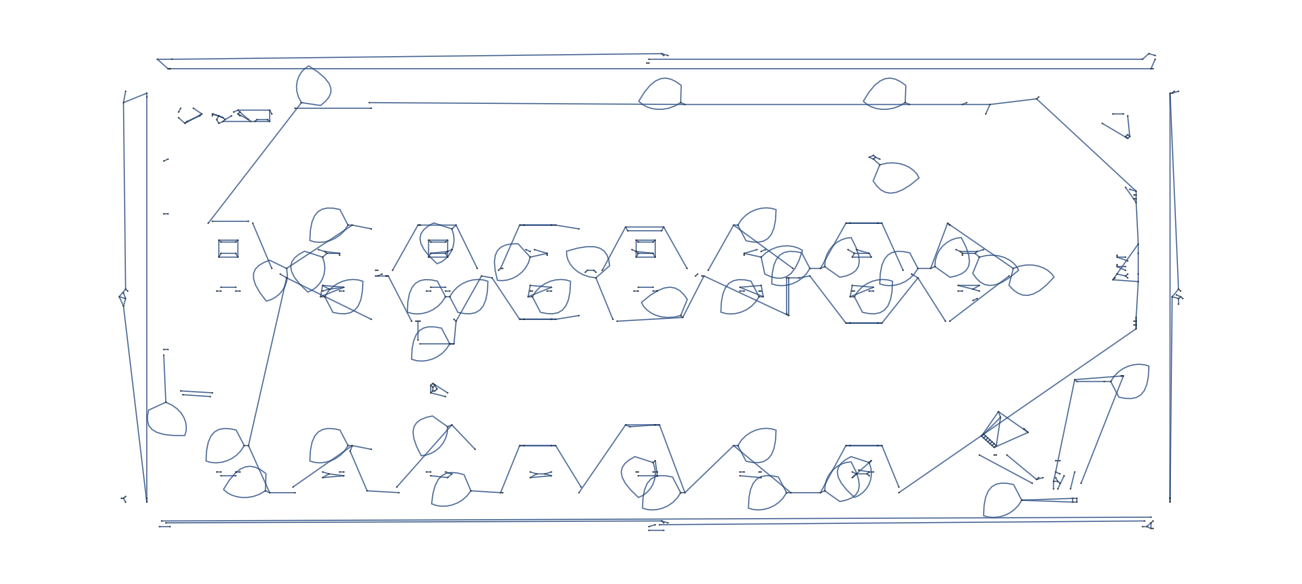

```mathematica
HighlightGraph[-Graphics-,PathGraph[FindShortestPath[-Graphics-,1,c]]]
```